```mathematica
(* Run 3_Fib_C62_relations first! *)
```

# Calculation of the ABC-equation for perfect tangles in Fib

## Definitions

## Install TriCat package by Stiegemann and load adjacency matrices and relations for morphisms in C_6

```mathematica
(*Install Library for trivalent Categories*)
SetDirectory[NotebookDirectory[]];
<<TriCats`;
(*Load Elements from C4 of a cubic trivalent category*)
LoadLibrary["stdlib"]
C4=Retrieve["C4Atoms"];
```

```mathematica
nullspace62=Import[FileNameJoin[{NotebookDirectory[],"nullspace62.m"}]];
C61=Import[FileNameJoin[{NotebookDirectory[],"C61.m"}]];
C62=Import[FileNameJoin[{NotebookDirectory[],"C62.m"}]];
```

## Define basis, operators and parameters

```mathematica
(*Define function which moves legs of every Diagram in a list of diagrams down*)
DiagramsMoveAllDown[diagramList_,newIngoingLegs_]:=Module[{MovedDiagramList},
MovedDiagramList={};
For[i=1,i≤Length[diagramList],i++,MovedDiagramList=AppendTo[MovedDiagramList,DiagramMoveDown[diagramList[[i]],newIngoingLegs]]];
Return[MovedDiagramList]
]
```

```mathematica
(*Define Basis of C4 of cubic trivalent category*)
C4Basis=DiagramsMoveAllDown[C4,2][[1;;2]];
```

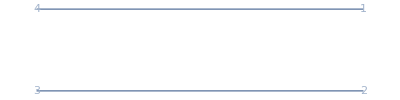
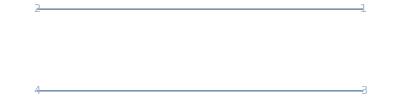
{Diagram[-Graphics-,{4,3},{1,2}],Diagram[-Graphics-,{4,3},{1,2}]}

```mathematica
EnsureGraph[C4Basis]
```

```mathematica
(*Define operators in basis representation*)
Clear[a1,a2,b1,b2,c1,c2,d1,d2,t1,t2];
OpA=a1*C4Basis[[1]]+a2*C4Basis[[2]];
OpB=b1*C4Basis[[1]]+b2*C4Basis[[2]];
OpC=c1*C4Basis[[1]]+c2*C4Basis[[2]];
OpD=d1*C4Basis[[1]]+d2*C4Basis[[2]];
(*d=2*Cos[Pi/5]*)
OpTplus=t1*C4Basis[[1]]+t2*C4Basis[[2]]/.{t1->1,t2->Exp[I*Pi*4/5]};
OpTminus=t1*C4Basis[[1]]+t2*C4Basis[[2]]/.{t1->1,t2->Exp[-I*Pi*4/5]};
```

```mathematica
(*Definition of the parameters of the trivalent category. Here: Fib*)
bigon=1;
loop=1/2 (1+√5);
triangle=1/2 (1-√5);
```

```mathematica
(*Define basis for C6 in Fib*)
C6Basis=C61[[1;;5]];
```

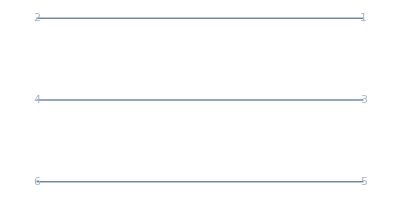
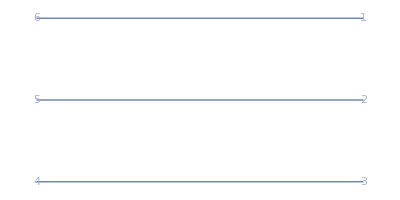
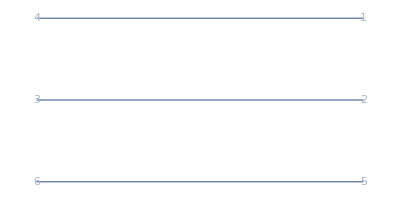
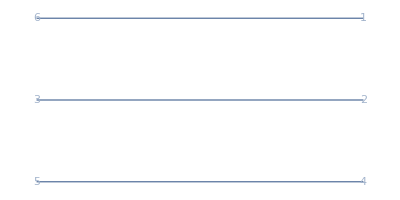
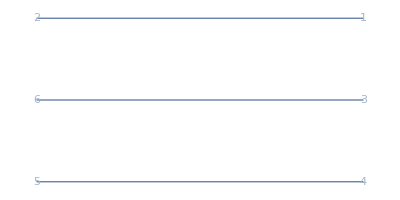
{Diagram[-Graphics-,{},{1,2,3,4,5,6}],Diagram[-Graphics-,{},{1,2,3,4,5,6}],Diagram[-Graphics-,{},{1,2,3,4,5,6}],Diagram[-Graphics-,{},{1,2,3,4,5,6}],Diagram[-Graphics-,{},{1,2,3,4,5,6}]}

```mathematica
EnsureGraph[C6Basis]
```

## Define function which replaces linear dependent diagrams in C(6,2) by corresponding basis representation

```mathematica
(*This function replaces all diagrams which are no basis elements of C6 by a linear combination of C6's basis elements*)
ReplaceKernDiagrams[diagram_]:=Module[{KernDiagrams,KernDiagramsInOut,DiagramList,ingoingLegs,ReplacementRules,ReplacedDiagramList,ReplacedDiagram,NormalDiagramList,DistinctList,ReplaceWrongForm},
DiagramList=List@@ExpandAll[diagram];
ingoingLegs=Length[DistinctDiagrams[List@@diagram][[1]][[2]]];
KernDiagrams=C62[[Length[C6Basis]+1;;Length[C62]]];
KernDiagramsInOut=DiagramsMoveAllDown[KernDiagrams,ingoingLegs];
ReplacementRules=KernDiagramsInOut;
For[i=1,i≤Length[KernDiagramsInOut],i++,ReplacementRules=ReplacePart[ReplacementRules,i->(KernDiagramsInOut[[i]]->(Sum[nullspace62[[i]][[j]]*DiagramMoveDown[C6Basis[[j]],ingoingLegs],{j,Length[C6Basis]}]) )]];
DistinctList={};
For[i=1,i≤Length[DiagramList],i++,DistinctList=AppendTo[DistinctList,DeleteCases[List@@DiagramList[[i]],Except[_Diagram]][[1]]]];
DistinctList=DeleteDuplicates[DistinctList];
ReplaceWrongForm={};
For[i=1,i≤Length[DistinctList],i++,For[j=1,j≤Length[KernDiagramsInOut],j++,If[IsomorphicDiagramQ[DistinctList[[i]],KernDiagramsInOut[[j]]]==True,ReplaceWrongForm=AppendTo[ReplaceWrongForm,DistinctList[[i]]->KernDiagramsInOut[[j]]]]]];
NormalDiagramList=DiagramList/.ReplaceWrongForm;
ReplacedDiagramList=NormalDiagramList/.ReplacementRules;
ReplacedDiagram=Total[ReplacedDiagramList];
Return[ReplacedDiagram]
];
```

## Calculations

## Calculate the case Tangle4 = Tangle0 to get a solution for A in terms of the other parameters

```mathematica
(*Definition of the case where tangle intersects all four legs*)
Tangle4=ReduceDiagram[
DiagramCompose[
DiagramTensor[Retrieve["Line"],Retrieve["Cup"],Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpA,OpD],
DiagramCompose[
DiagramTensor[Retrieve["Line"],OpTplus,Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpB,OpC],
DiagramTensor[Retrieve["Line"],Retrieve["Cap"],Retrieve["Line"]]
]
]
]
]
,b->bigon,d-> loop,t-> triangle];
```

```mathematica
(*Calculate Solution*)
T4Comp=Components[Tangle4,C4Basis]/.d->loop;
TComp=Components[OpTplus,C4Basis]/.d->loop;
```

```mathematica
Solution40=Solve[T4Comp==TComp*loop,{a1,a2}];
```

```mathematica
a1Sol=Solution40[[1,1,2]]
```

-((-1/2 (1+√5) ⅇ^((4 ⅈ π)/5) (b1 c1 d1+1/2 (1+√5) b2 c1 d1+1/2 (1+√5) b1 c1 d1 ⅇ^((4 ⅈ π)/5)+b2 c1 d1 ⅇ^((4 ⅈ π)/5)+b1 c2 d1 ⅇ^((4 ⅈ π)/5))-1/2 (-1-√5) (b1 c2 d1+1/2 (1+√5) b2 c2 d1+b1 c1 d2+1/2 (1+√5) b2 c1 d2+1/2 (1+√5) b1 c2 d2+1/4 (1+√5)^2 b2 c2 d2+b2 c2 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b1 c1 d2 ⅇ^((4 ⅈ π)/5)+b2 c1 d2 ⅇ^((4 ⅈ π)/5)+b1 c2 d2 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b2 c2 d2 ⅇ^((4 ⅈ π)/5)))/((b1 c1 d1+1/2 (1+√5) b2 c1 d1+1/2 (1+√5) b1 c1 d1 ⅇ^((4 ⅈ π)/5)+b2 c1 d1 ⅇ^((4 ⅈ π)/5)+b1 c2 d1 ⅇ^((4 ⅈ π)/5)) (b2 c2 d1+b2 c1 d2+1/2 (1+√5) b2 c2 d2+1/2 (1+√5) b2 c2 d1 ⅇ^((4 ⅈ π)/5)+b2 c2 d2 ⅇ^((4 ⅈ π)/5))-(1/2 (1+√5) b1 c1 d1+b2 c1 d1+b1 c2 d1+b1 c1 d2+1/2 (1+√5) b1 c2 d2+1/4 (1+√5)^2 b1 c1 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b2 c1 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b1 c2 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b1 c1 d2 ⅇ^((4 ⅈ π)/5)+b2 c1 d2 ⅇ^((4 ⅈ π)/5)+b1 c2 d2 ⅇ^((4 ⅈ π)/5)) (b1 c2 d1+1/2 (1+√5) b2 c2 d1+b1 c1 d2+1/2 (1+√5) b2 c1 d2+1/2 (1+√5) b1 c2 d2+1/4 (1+√5)^2 b2 c2 d2+b2 c2 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b1 c1 d2 ⅇ^((4 ⅈ π)/5)+b2 c1 d2 ⅇ^((4 ⅈ π)/5)+b1 c2 d2 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b2 c2 d2 ⅇ^((4 ⅈ π)/5))))

```mathematica
Export["a1Sol.m",a1Sol];
```

```mathematica
a2Sol=Solution40[[1,2,2]]
```

-(-1-√5)/((2 b1 c1+(-1)^(4/5) b1 c1+(-1)^(4/5) √5 b1 c1+b2 c1+2 (-1)^(4/5) b2 c1+√5 b2 c1+2 (-1)^(4/5) b1 c2) d1)+((b1 c1 d1+3 (-1)^(4/5) b1 c1 d1+√5 b1 c1 d1+(-1)^(4/5) √5 b1 c1 d1+2 b2 c1 d1+(-1)^(4/5) b2 c1 d1+(-1)^(4/5) √5 b2 c1 d1+2 b1 c2 d1+(-1)^(4/5) b1 c2 d1+(-1)^(4/5) √5 b1 c2 d1+2 b1 c1 d2+(-1)^(4/5) b1 c1 d2+(-1)^(4/5) √5 b1 c1 d2+2 (-1)^(4/5) b2 c1 d2+b1 c2 d2+2 (-1)^(4/5) b1 c2 d2+√5 b1 c2 d2) (-1/2 (1+√5) ⅇ^((4 ⅈ π)/5) (b1 c1 d1+1/2 (1+√5) b2 c1 d1+1/2 (1+√5) b1 c1 d1 ⅇ^((4 ⅈ π)/5)+b2 c1 d1 ⅇ^((4 ⅈ π)/5)+b1 c2 d1 ⅇ^((4 ⅈ π)/5))-1/2 (-1-√5) (b1 c2 d1+1/2 (1+√5) b2 c2 d1+b1 c1 d2+1/2 (1+√5) b2 c1 d2+1/2 (1+√5) b1 c2 d2+1/4 (1+√5)^2 b2 c2 d2+b2 c2 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b1 c1 d2 ⅇ^((4 ⅈ π)/5)+b2 c1 d2 ⅇ^((4 ⅈ π)/5)+b1 c2 d2 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b2 c2 d2 ⅇ^((4 ⅈ π)/5))))/((2 b1 c1+(-1)^(4/5) b1 c1+(-1)^(4/5) √5 b1 c1+b2 c1+2 (-1)^(4/5) b2 c1+√5 b2 c1+2 (-1)^(4/5) b1 c2) d1 ((b1 c1 d1+1/2 (1+√5) b2 c1 d1+1/2 (1+√5) b1 c1 d1 ⅇ^((4 ⅈ π)/5)+b2 c1 d1 ⅇ^((4 ⅈ π)/5)+b1 c2 d1 ⅇ^((4 ⅈ π)/5)) (b2 c2 d1+b2 c1 d2+1/2 (1+√5) b2 c2 d2+1/2 (1+√5) b2 c2 d1 ⅇ^((4 ⅈ π)/5)+b2 c2 d2 ⅇ^((4 ⅈ π)/5))-(1/2 (1+√5) b1 c1 d1+b2 c1 d1+b1 c2 d1+b1 c1 d2+1/2 (1+√5) b1 c2 d2+1/4 (1+√5)^2 b1 c1 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b2 c1 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b1 c2 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b1 c1 d2 ⅇ^((4 ⅈ π)/5)+b2 c1 d2 ⅇ^((4 ⅈ π)/5)+b1 c2 d2 ⅇ^((4 ⅈ π)/5)) (b1 c2 d1+1/2 (1+√5) b2 c2 d1+b1 c1 d2+1/2 (1+√5) b2 c1 d2+1/2 (1+√5) b1 c2 d2+1/4 (1+√5)^2 b2 c2 d2+b2 c2 d1 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b1 c1 d2 ⅇ^((4 ⅈ π)/5)+b2 c1 d2 ⅇ^((4 ⅈ π)/5)+b1 c2 d2 ⅇ^((4 ⅈ π)/5)+1/2 (1+√5) b2 c2 d2 ⅇ^((4 ⅈ π)/5))))

```mathematica
Export["a2Sol.m",a2Sol];
```

## Calculate the case Tangle3 = Tangle1

```mathematica
(*Definition of the case where tangle intersects 3 legs*)
Tangle3=ReduceDiagram[
DiagramCompose[
DiagramTensor[OpA,Retrieve["Line"],Retrieve["Line"]],
DiagramCompose[
DiagramTensor[Retrieve["Line"],OpTplus,Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpB,OpC],
DiagramTensor[Retrieve["Line"],Retrieve["Cap"],Retrieve["Line"]]
]
]
]
,{b->bigon,t-> triangle,d-> loop}];
```

```mathematica
(*Definition of the case where tangle intersects 1 leg*)
Tangle1=ReduceDiagram[
DiagramCompose[
DiagramTensor[Retrieve["Line"],OpD,Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpTplus,Retrieve["Line"],Retrieve["Line"]],
DiagramTensor[Retrieve["Line"],Retrieve["Line"],Retrieve["Cap"]]
]
]
,{b->bigon,t-> triangle,d-> loop}];
```

```mathematica
(*Calculate solution*)
T1Comp=Components[ReplaceKernDiagrams[Tangle1],DiagramsMoveAllDown[C6Basis,4]]/.d->loop;
T3Comp=Components[ReplaceKernDiagrams[Tangle3],DiagramsMoveAllDown[C6Basis,4]]/.d->loop;
```

```mathematica
T3Comp=Simplify[T3Comp];
T3Comp=FullSimplify[T3Comp];
```

```mathematica
Export["T1Comp_Trep.m",T1Comp];
Export["T3Comp_simpl_Trep.m",T3Comp];
```

```mathematica
Solution31=Solve[T1Comp==T3Comp,{a1,a2,b1,b2,c1,c2,d1,d2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a1→-(-1)^(1/5) a2,c2→(-1)^(4/5) c1,d1→1/2 ((-1)^(1/5) a2 b1 c1-2 (-1)^(2/5) a2 b1 c1+(-1)^(1/5) √5 a2 b1 c1),d2→(a2 b2 c1-(-1)^(3/5) a2 b2 c1+5 (-1)^(4/5) a2 b2 c1+√5 a2 b2 c1-(-1)^(3/5) √5 a2 b2 c1+(-1)^(4/5) √5 a2 b2 c1)/(-1+2 (-1)^(1/5)-√5)},{a1→0,a2→0,d1→0,d2→0},{b1→0,b2→0,d1→0,d2→0},{b2→(-1)^(4/5) b1,c2→(-a1 c1-a2 c1+(-1)^(1/5) a2 c1-(-1)^(4/5) a2 c1-√5 a2 c1)/a2,d1→-a1 b1 c1+(-1)^(1/5) a1 b1 c1-(-1)^(4/5) a1 b1 c1-√5 a1 b1 c1-(a1^2 b1 c1)/a2,d2→-(-1)^(4/5) (a1 b1 c1-(-1)^(1/5) a1 b1 c1+(-1)^(4/5) a1 b1 c1+√5 a1 b1 c1+(a1^2 b1 c1)/a2)},{c1→0,c2→0,d1→0,d2→0},{a2→0,b1→0,b2→0,d1→0,d2→0},{a1→0,a2→0,b2→-(-1)^(2/5) b1,d1→0,d2→0},{a1→0,a2→0,b2→(-1)^(4/5) b1,d1→0,d2→0},{a1→0,a2→0,c1→0,d1→0,d2→0},{a2→0,b2→(-1)^(4/5) b1,c1→0,d1→a1 b1 c2,d2→(-1)^(4/5) a1 b1 c2},{a2→0,c1→0,c2→0,d1→0,d2→0},{a1→(-4 (-1)^(1/5) a2+7 (-1)^(2/5) a2-6 (-1)^(3/5) a2+(-1)^(4/5) a2-2 (-1)^(1/5) √5 a2+5 (-1)^(2/5) √5 a2-4 (-1)^(3/5) √5 a2+(-1)^(4/5) √5 a2)/(3-(-1)^(1/5)-2 (-1)^(2/5)+(-1)^(3/5)+2 (-1)^(4/5)-√5+(-1)^(1/5) √5-2 (-1)^(2/5) √5+3 (-1)^(3/5) √5-2 (-1)^(4/5) √5),b1→0,c2→(-21 c1+3 (-1)^(1/5) c1-3 (-1)^(2/5) c1+22 (-1)^(3/5) c1-32 (-1)^(4/5) c1-5 √5 c1-3 (-1)^(1/5) √5 c1+(-1)^(2/5) √5 c1+8 (-1)^(3/5) √5 c1-12 (-1)^(4/5) √5 c1)/(14-20 (-1)^(1/5)+17 (-1)^(2/5)-10 (-1)^(3/5)+8 (-1)^(4/5)-2 √5-2 (-1)^(1/5) √5+(-1)^(2/5) √5+4 (-1)^(3/5) √5-6 (-1)^(4/5) √5),d1→0,d2→(a2 b2 c1-(-1)^(1/5) a2 b2 c1-(-1)^(2/5) a2 b2 c1+2 (-1)^(3/5) a2 b2 c1+√5 a2 b2 c1-(-1)^(1/5) √5 a2 b2 c1+(-1)^(2/5) √5 a2 b2 c1)/(2 ((-1)^(1/5)-(-1)^(2/5)+(-1)^(3/5)))},{a1→0,b2→-(-1)^(2/5) b1,c2→0,d1→0,d2→0},{a1→(5167024477123 a2-5167812457619 (-1)^(1/5) a2+5168210388465 (-1)^(2/5) a2-5166778542335 (-1)^(3/5) a2+5168697387194 (-1)^(4/5) a2+2309411065245 √5 a2-2308819039823 (-1)^(1/5) √5 a2+2308789179119 (-1)^(2/5) √5 a2-2309429520175 (-1)^(3/5) √5 a2+2308423287286 (-1)^(4/5) √5 a2)/(16713565122224-16712003773773 (-1)^(1/5)+16712515444548 (-1)^(2/5)-16713248892294 (-1)^(3/5)+16711550478137 (-1)^(4/5)+7476129886172 √5-7476976241807 (-1)^(1/5) √5+7476747415680 (-1)^(2/5) √5-7476271308496 (-1)^(3/5) √5+7477270492229 (-1)^(4/5) √5),b2→-(-1)^(2/5) b1,c2→(-204820 c1+215766 (-1)^(1/5) c1-204820 (-1)^(2/5) c1+211585 (-1)^(3/5) c1-211585 (-1)^(4/5) c1)/(-211585+204820 (-1)^(1/5)-215766 (-1)^(2/5)+204820 (-1)^(3/5)-211585 (-1)^(4/5)),d1→a2 b1 c1,d2→(3517929664756 a2 b1 c1-3519064567926 (-1)^(1/5) a2 b1 c1+3517929664756 (-1)^(2/5) a2 b1 c1-3518631073489 (-1)^(3/5) a2 b1 c1+3518631073489 (-1)^(4/5) a2 b1 c1)/(-3517929664756+3518631073489 (-1)^(1/5)-3518631073489 (-1)^(2/5)+3517929664756 (-1)^(3/5)-3519064567926 (-1)^(4/5))},{b1→0,b2→0,c1→0,d1→0,d2→0},{b1→0,c1→0,c2→0,d1→0,d2→0}}

## Calculate the case Tangle2AD = Tangle2BC

```mathematica
(*Definition of the case where tangle intersects the 2 lower legs*)
Tangle2AD=ReduceDiagram[
DiagramCompose[
DiagramTensor[Retrieve["Line"],Retrieve["Cup"],Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpA,OpD],
DiagramTensor[Retrieve["Line"],OpTplus,Retrieve["Line"]]
]
]
,b->bigon,d-> loop,t-> triangle];
```

```mathematica
(*Definition of the case where tangle intersects the 2 upper legs*)
Tangle2BC=ReduceDiagram[
DiagramCompose[
DiagramTensor[Retrieve["Cup"],Retrieve["Line"],Retrieve["Line"],Retrieve["Cup"]],
DiagramCompose[
DiagramTensor[Retrieve["Line"],Retrieve["Line"],OpTplus,Retrieve["Line"],Retrieve["Line"]],
DiagramCompose[
DiagramTensor[Retrieve["Line"],OpB,OpC,Retrieve["Line"]],
DiagramTensor[Retrieve["Line"],Retrieve["Line"],Retrieve["Cap"],Retrieve["Line"],Retrieve["Line"]]
]
]
]
,b->bigon,d-> loop,t-> triangle];
```

```mathematica
(*Calculate solution*)
T2ADComp=Components[ReplaceKernDiagrams[Tangle2AD],DiagramsMoveAllDown[C6Basis,2]]/.d->loop;
T2BCComp=Components[ReplaceKernDiagrams[Tangle2BC],DiagramsMoveAllDown[C6Basis,2]]/.d->loop;
```

```mathematica
T2ADComp=Simplify[T2ADComp];
T2ADComp=FullSimplify[T2ADComp];
T2BCComp=Simplify[T2BCComp];
T2BCComp=FullSimplify[T2BCComp];
```

```mathematica
Export["T2ADComp_Trep.m",T2ADComp];
Export["T2BCComp_Trep.m",T2BCComp];
```

```mathematica
Solution22=Solve[T2ADComp==T2BCComp,{a1,a2,b1,b2,c1,c2,d1,d2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a1→0,a2→0,b1→0,b2→0},{a1→0,a2→0,c1→0,c2→0},{b1→0,b2→0,d1→0,d2→0},{c1→0,c2→0,d1→0,d2→0},{a1→-(-1)^(1/5) a2,c1→-(-1)^(1/5) c2,d1→(b1 c2)/a2,d2→(b2 c2)/a2},{b1→-(-1)^(1/5) b2,c1→(a1 c2)/a2,d1→-((-1)^(1/5) b2 c2)/a2,d2→(b2 c2)/a2},{a1→0,a2→0,b1→0,b2→0,c2→0},{a1→0,a2→0,b2→0,c1→0,c2→0},{a1→0,a2→0,b1→0,b2→0,d2→0},{a2→0,b1→0,b2→0,d1→0,d2→0},{a2→0,b1→-(-1)^(1/5) b2,c1→(a1 d2)/b2,c2→0,d1→-(-1)^(1/5) d2},{a1→0,a2→0,c1→0,c2→0,d2→0},{a2→0,c1→0,c2→0,d1→0,d2→0},{b1→0,b2→0,c2→0,d1→0,d2→0},{a1→-(-1)^(1/5) a2,b1→0,b2→0,d1→0,d2→0},{b1→0,c1→0,c2→0,d1→0,d2→0},{a1→-(-1)^(1/5) a2,b1→0,c1→-(-1)^(1/5) c2,d1→0,d2→(b2 c2)/a2},{a1→0,a2→0,b1→0,b2→0,c2→0,d2→0},{a1→0,a2→0,b2→0,c1→0,c2→0,d2→0},{a2→0,b1→0,b2→0,c2→0,d1→0,d2→0},{a2→0,b2→0,c1→0,c2→0,d1→0,d2→0}}

## Compare and interpret solutions

```mathematica
(*Function which turns the output of Solve into a list of solutions*)
SolveToList[Solution_,Parameters_]:=Module[{i,j,SolutionList={},SingleSolution,Pos},
For[i=1,i≤Length[Solution],i++,
SingleSolution=Parameters;
For[j=1,j≤Length[Solution[[i]]],j++,
Pos=Position[Parameters,Solution[[i,j,1]]][[1]];
SingleSolution=ReplacePart[SingleSolution,Pos->Solution[[i,j,2]]];
](*For*);
SolutionList=AppendTo[SolutionList,SingleSolution];
](*For*);
Return[SolutionList];
];
```

```mathematica
(*Calculate Solution of both equation 31 and 22*)
Block[{i,j,iSol,Solve3122},
Solve3122={};
For[i=1,i≤Length[Solution22],i++,
iSol=Solve[(T1Comp/.Solution22[[i]])==(T3Comp/.Solution22[[i]]),{a1,a2,b1,b2,c1,c2,d1,d2}];
AppendTo[Solve3122,iSol];
](*For*);
Solution3122={};
For[i=1,i≤Length[Solution22],i++,
If[Solve3122[[i]]≠{{}},
For[j=1,j≤Length[Solve3122[[i]]],j++,
Solution3122=AppendTo[Solution3122,Join[Solution22[[i]]/.Solve3122[[i,j]],Solve3122[[i,j]]]];
](*For*);
](*If*);
](*For*)
](*Block*);
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

```mathematica
(*Eliminate solutions where one operator is zero*)
Block[{i},
deleteSol={};
For[i=1,i≤Length[Solution3122],i++,
If[MemberQ[Solution3122[[i]],a1->0]==True&&MemberQ[Solution3122[[i]],a2->0]==True,
AppendTo[deleteSol,Append[Solution3122[[i]],delete]],
If[MemberQ[Solution3122[[i]],b1->0]==True&&MemberQ[Solution3122[[i]],b2->0]==True,
AppendTo[deleteSol,Append[Solution3122[[i]],delete]],
If[MemberQ[Solution3122[[i]],c1->0]==True&&MemberQ[Solution3122[[i]],c2->0]==True,
AppendTo[deleteSol,Append[Solution3122[[i]],delete]],
If[MemberQ[Solution3122[[i]],d1->0]==True&&MemberQ[Solution3122[[i]],d2->0]==True,
AppendTo[deleteSol,Append[Solution3122[[i]],delete]],
AppendTo[deleteSol,Solution3122[[i]]];
](*If d1->0 & d2->0*);
](*If c1->0 & c2->0*);
](*If b1->0 & b2->0*);
](*If a1->0 & a2->0*);
](*For*);
NonTrivialSolution3122={};
For[i=1,i≤Length[deleteSol],i++,
If[MemberQ[deleteSol[[i]],delete]==False,
AppendTo[NonTrivialSolution3122,deleteSol[[i]]];
](*If*);
](*For*);
NonTrivialSolution3122=FullSimplify[NonTrivialSolution3122];
](*Block*);
```

```mathematica
(*We have 6 nontrivial solutions to equations 31 AND 22:*)
Length[NonTrivialSolution3122]
```

6

```mathematica
NonTrivialSolution3122
```

{{a1→(-1)^(3/5),c1→-(-1)^(1/5) c2,d1→(-1)^(3/5) b1 c2,d2→(-1)^(3/5) b2 c2,a2→-(-1)^(2/5)},{a1→-(-1)^(3/5),c1→-(-1)^(1/5) c2,d1→-(-1)^(3/5) b1 c2,d2→-(-1)^(3/5) b2 c2,a2→(-1)^(2/5)},{b1→-(-1)^(1/5) b2,c1→(-1)^(4/5) c2,d1→(-1)^(3/5) b2 c2,d2→-(-1)^(2/5) b2 c2,a1→-(-1)^(2/5),a2→(-1)^(3/5)},{b1→-(-1)^(1/5) b2,c1→(-1)^(4/5) c2,d1→-(-1)^(3/5) b2 c2,d2→(-1)^(2/5) b2 c2,a1→(-1)^(2/5),a2→-(-1)^(3/5)},{b1→-(-1)^(1/5) b2,c1→-(-1)^(1/5) c2,d1→-(-1)^(4/5) b2 c2,d2→(-1)^(3/5) b2 c2,a1→(-1)^(3/5),a2→-(-1)^(2/5)},{b1→-(-1)^(1/5) b2,c1→-(-1)^(1/5) c2,d1→(-1)^(4/5) b2 c2,d2→-(-1)^(3/5) b2 c2,a1→-(-1)^(3/5),a2→(-1)^(2/5)}}

```mathematica
(*Function which finds parameters in the solution which are yet unsolved*)
FindMissingParameters[Solution_]:=Module[{i,j,ParameterList,AllParameters,UnsolvedParameters},
UnsolvedParameters={};
AllParameters={a1,a2,b1,b2,c1,c2,d1,d2};
For[i=1,i≤Length[Solution],i++,
ParameterList={};
For[j=1,j≤Length[Solution[[i]]],j++,
AppendTo[ParameterList,Solution[[i,j,1]]];
](*For*);
AppendTo[UnsolvedParameters,Complement[AllParameters,ParameterList]];
](*For*);
Return[UnsolvedParameters]
](*Module*);
```

```mathematica
(*Calculate unsolved parameters in each solution*)
UnsolvedParameters=FindMissingParameters[NonTrivialSolution3122]
```

{{b1,b2,c2},{b1,b2,c2},{b2,c2},{b2,c2},{b2,c2},{b2,c2}}

```mathematica
(*Find solutions which fulfill ALL equations*)
Block[{i},
AllSolutions={};
For[i=1,i≤Length[NonTrivialSolution3122],i++,
AppendTo[
AllSolutions,
FullSimplify[
Solve[(TComp/.NonTrivialSolution3122[[i]])==(T4Comp/.NonTrivialSolution3122[[i]])/loop,UnsolvedParameters[[i]]]
](*FullSimplify*)
](*AppendTo*);
](*For*);
](*Block*);
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

```mathematica
ToRadicals[AllSolutions]
```

{{{b2→-1/2 (1+√5) b1-(√(1/2 (-3-√5+ⅈ √(2 (5+√5))) c2^2+(1+√5) b1^2 c2^4))/(√2 c2^2)},{b2→-1/2 (1+√5) b1+(√(-(3+√5-ⅈ √(2 (5+√5))) c2^2+2 (1+√5) b1^2 c2^4))/(2 c2^2)}},{{b2→-1/2 (1+√5) b1-(√(1/2 (-3-√5+ⅈ √(2 (5+√5))) c2^2+(1+√5) b1^2 c2^4))/(√2 c2^2)},{b2→-1/2 (1+√5) b1+(√(-(3+√5-ⅈ √(2 (5+√5))) c2^2+2 (1+√5) b1^2 c2^4))/(2 c2^2)}},{{c2→-(-1)^(2/5)/(√((-1)^(4/5) b2^2))},{c2→(-1)^(2/5)/(√((-1)^(4/5) b2^2))}},{{c2→-(-1)^(2/5)/(√((-1)^(4/5) b2^2))},{c2→(-1)^(2/5)/(√((-1)^(4/5) b2^2))}},{{c2→-(-1)^(2/5)/(√(-(-1)^(1/5) b2^2))},{c2→((-(-1)^(1/5) b2^2)^(3/2))/b2^4}},{{c2→-(-1)^(2/5)/(√(-(-1)^(1/5) b2^2))},{c2→((-(-1)^(1/5) b2^2)^(3/2))/b2^4}}}

```mathematica
(*Create list which contains solutions*)
Block[{i,j},
FibSolution={};
For[i=1,i≤Length[AllSolutions],i++,
If[AllSolutions[[i]]≠{},
For[j=1,j≤Length[AllSolutions[[i]]],j++,
AppendTo[FibSolution,Join[FullSimplify[NonTrivialSolution3122[[i]]/.AllSolutions[[i,j]]],AllSolutions[[i,j]]]];
](*For*);
](*If*);
](*For*);
](*Block*);
```

```mathematica
ToRadicals[FibSolution]
```

{{a1→(-1)^(3/5),c1→-(-1)^(1/5) c2,d1→(-1)^(3/5) b1 c2,d2→-((-1)^(3/5) ((1+√5) b1 c2^2+√2 √(c2^2 (1/2 (-3-√5+ⅈ √(2 (5+√5)))+(1+√5) b1^2 c2^2))))/(2 c2),a2→-(-1)^(2/5),b2→-1/2 (1+√5) b1-(√(1/2 (-3-√5+ⅈ √(2 (5+√5))) c2^2+(1+√5) b1^2 c2^4))/(√2 c2^2)},{a1→(-1)^(3/5),c1→-(-1)^(1/5) c2,d1→(-1)^(3/5) b1 c2,d2→((-1)^(3/5) (-(1+√5) b1 c2^2+√(-(3+√5-ⅈ √(2 (5+√5))) c2^2+2 (1+√5) b1^2 c2^4)))/(2 c2),a2→-(-1)^(2/5),b2→-1/2 (1+√5) b1+(√(-(3+√5-ⅈ √(2 (5+√5))) c2^2+2 (1+√5) b1^2 c2^4))/(2 c2^2)},{a1→-(-1)^(3/5),c1→-(-1)^(1/5) c2,d1→-(-1)^(3/5) b1 c2,d2→((-1)^(3/5) ((1+√5) b1 c2^2+√2 √(c2^2 (1/2 (-3-√5+ⅈ √(2 (5+√5)))+(1+√5) b1^2 c2^2))))/(2 c2),a2→(-1)^(2/5),b2→-1/2 (1+√5) b1-(√(1/2 (-3-√5+ⅈ √(2 (5+√5))) c2^2+(1+√5) b1^2 c2^4))/(√2 c2^2)},{a1→-(-1)^(3/5),c1→-(-1)^(1/5) c2,d1→-(-1)^(3/5) b1 c2,d2→((-1)^(3/5) ((1+√5) b1 c2^2-√(-(3+√5-ⅈ √(2 (5+√5))) c2^2+2 (1+√5) b1^2 c2^4)))/(2 c2),a2→(-1)^(2/5),b2→-1/2 (1+√5) b1+(√(-(3+√5-ⅈ √(2 (5+√5))) c2^2+2 (1+√5) b1^2 c2^4))/(2 c2^2)},{b1→-(-1)^(1/5) b2,c1→-b2^2/(((-1)^(4/5) b2^2)^(3/2)),d1→b2/(√((-1)^(4/5) b2^2)),d2→(√((-1)^(4/5) b2^2))/b2,a1→-(-1)^(2/5),a2→(-1)^(3/5),c2→-(-1)^(2/5)/(√((-1)^(4/5) b2^2))},{b1→-(-1)^(1/5) b2,c1→b2^2/(((-1)^(4/5) b2^2)^(3/2)),d1→-b2/(√((-1)^(4/5) b2^2)),d2→-(√((-1)^(4/5) b2^2))/b2,a1→-(-1)^(2/5),a2→(-1)^(3/5),c2→(-1)^(2/5)/(√((-1)^(4/5) b2^2))},{b1→-(-1)^(1/5) b2,c1→-b2^2/(((-1)^(4/5) b2^2)^(3/2)),d1→-b2/(√((-1)^(4/5) b2^2)),d2→-(√((-1)^(4/5) b2^2))/b2,a1→(-1)^(2/5),a2→-(-1)^(3/5),c2→-(-1)^(2/5)/(√((-1)^(4/5) b2^2))},{b1→-(-1)^(1/5) b2,c1→b2^2/(((-1)^(4/5) b2^2)^(3/2)),d1→b2/(√((-1)^(4/5) b2^2)),d2→(√((-1)^(4/5) b2^2))/b2,a1→(-1)^(2/5),a2→-(-1)^(3/5),c2→(-1)^(2/5)/(√((-1)^(4/5) b2^2))},{b1→-(-1)^(1/5) b2,c1→(-1)^(3/5)/(√(-(-1)^(1/5) b2^2)),d1→(√(-(-1)^(1/5) b2^2))/b2,d2→b2/(√(-(-1)^(1/5) b2^2)),a1→(-1)^(3/5),a2→-(-1)^(2/5),c2→-(-1)^(2/5)/(√(-(-1)^(1/5) b2^2))},{b1→-(-1)^(1/5) b2,c1→((-(-1)^(1/5) b2^2)^(5/2))/b2^6,d1→-(√(-(-1)^(1/5) b2^2))/b2,d2→-b2/(√(-(-1)^(1/5) b2^2)),a1→(-1)^(3/5),a2→-(-1)^(2/5),c2→((-(-1)^(1/5) b2^2)^(3/2))/b2^4},{b1→-(-1)^(1/5) b2,c1→(-1)^(3/5)/(√(-(-1)^(1/5) b2^2)),d1→-(√(-(-1)^(1/5) b2^2))/b2,d2→-b2/(√(-(-1)^(1/5) b2^2)),a1→-(-1)^(3/5),a2→(-1)^(2/5),c2→-(-1)^(2/5)/(√(-(-1)^(1/5) b2^2))},{b1→-(-1)^(1/5) b2,c1→((-(-1)^(1/5) b2^2)^(5/2))/b2^6,d1→(√(-(-1)^(1/5) b2^2))/b2,d2→b2/(√(-(-1)^(1/5) b2^2)),a1→-(-1)^(3/5),a2→(-1)^(2/5),c2→((-(-1)^(1/5) b2^2)^(3/2))/b2^4}}

## Compare with solution from braiding in SO(3)q

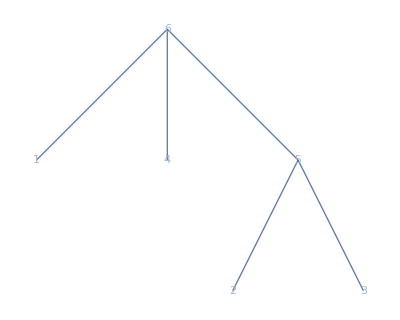
Diagram[-Graphics-,{4,3},{1,2}]/q^2+(-1+q^2) Diagram[-Graphics-,{4,3},{1,2}]-(1/q^2+q^2) Diagram[-Graphics-,{4,3},{1,2}]

```mathematica
(*Braiding in SO(3)q*)
Clear[q];
C4SO3q=DiagramsMoveAllDown[C4,2][[{1,2,4}]];
BraidingDiagram=(q^2-1)C4SO3q[[1]]+q^(-2)C4SO3q[[2]]-(q^2+q^(-2))C4SO3q[[3]];
EnsureGraph[BraidingDiagram]
```

```mathematica
(*Claculation of q in Fib*)
qFib=FullSimplify[Solve[{loop==(q^2)+1+q^(-2),triangle==((q^2)-1+q^(-2))/(q^2+q^(-2))},q]]
```

{{q→(-1)^(4/5)},{q→-(-1)^(4/5)},{q→-(-1)^(1/5)},{q→(-1)^(1/5)}}

```mathematica
(*It follows the braiding from Fib choosing q->(-1)^(1/5)*)
(*FibReplacementRule=C4SO3q[[3]]->(-2+d)/(-1+d)C4SO3q[[1]]+1/((-1+d) d)C4SO3q[[2]];*)
(*FibReplacementRule=C4SO3q[[3]]->d/(-1+d)C4SO3q[[1]]-(1-2 d)/((-1+d) d)*C4SO3q[[2]];*)
FibReplacementRule=C4SO3q[[3]]->(-2+d)/(-1+d)C4SO3q[[1]]+C4SO3q[[2]];
FibBraidingDiagram=FullSimplify[BraidingDiagram/.{FibReplacementRule,qFib[[4]]/.{polys__}:>(polys)}];
EnsureGraph[FibBraidingDiagram]
```

-(-1)^(2/5) Diagram[-Graphics-,{4,3},{1,2}]+((1+(-1)^(2/5)-2 (-1)^(3/5)+(-1+(-1)^(3/5)) d) Diagram[-Graphics-,{4,3},{1,2}])/(-1+d)

```mathematica
(*Claculate replacement rules for braiding solution*)
BraidingBasisRep=Components[FibBraidingDiagram,C4Basis];
BraidingReplacementRules={a1->BraidingBasisRep[[1]],a2->BraidingBasisRep[[2]],b1->BraidingBasisRep[[1]],b2->BraidingBasisRep[[2]],c1->BraidingBasisRep[[1]],c2->BraidingBasisRep[[2]],d1->BraidingBasisRep[[1]],d2->BraidingBasisRep[[2]]};
```

```mathematica
(*Insert braiding in the equations*)
(TComp/.BraidingReplacementRules)==FullSimplify[(T4Comp/.(BraidingReplacementRules/.d->loop))/loop]
```

True

```mathematica
FullSimplify[(T1Comp/.(BraidingReplacementRules/.d->loop))]==FullSimplify[(T3Comp/.(BraidingReplacementRules/.d->loop))]
```

True

```mathematica
FullSimplify[(T2ADComp/.(BraidingReplacementRules/.d->loop))]==FullSimplify[(T2BCComp/.(BraidingReplacementRules/.d->loop))]
```

True

```mathematica
(*Therefore, the braiding really solves our equations. Now compare the braiding solution with the solutions we found for Fib to answer the question which of the solutions corresponds to the braiding*)
```

```mathematica
(*To perform this task we need to be able to compare our solutions with the braiding solution. We introduce some auxiliary functions to define a function which compares the solutions*)
```

```mathematica
(*We create a list with the missing parameters in the right order with respect to the solution*)
MissingParameters=FindMissingParameters[FibSolution]
```

{{b1,c2},{b1,c2},{b1,c2},{b1,c2},{b2},{b2},{b2},{b2},{b2},{b2},{b2},{b2}}

```mathematica
(*Function which replaces the free parameters in each solution by the solution coming from braiding*)
BuildBraidingSolution[Solution_]:=Module[{i,j,BraidingSolution,ValueList,Replacement,BraidingSolutioni},
BraidingSolution={};
ValueList=FullSimplify[MissingParameters/.(BraidingReplacementRules/.d->loop)];

For[i=1,i≤Length[Solution],i++,
Replacement={};
For[j=1,j≤Length[MissingParameters[[i]]],j++,
AppendTo[Replacement,(MissingParameters[[i,j]])->(ValueList[[i,j]]/.{polys__}:>(polys))];
](*For j*);
BraidingSolutioni=FullSimplify[Append[FibSolution[[i]]/.Replacement,Replacement]];
AppendTo[BraidingSolution,Flatten[BraidingSolutioni]];
](*For i*);
Return[BraidingSolution];
](*Module*);
```

```mathematica
Block[{i,Sol},
FibBraidingSolution={};
Sol=BuildBraidingSolution[FibSolution];
For[i=1,i≤Length[Sol],i++,
AppendTo[FibBraidingSolution,Sort[Sol[[i]]]];
](*For*);
Print[ToRadicals[FibBraidingSolution]];
](*Block*);
```

{{a1→(-1)^(3/5),a2→-(-1)^(2/5),b1→(-1)^(3/5),b2→1/4 (3+√5-ⅈ √(10 (5+√5))),c1→(-1)^(3/5),c2→-(-1)^(2/5),d1→(-1)^(3/5),d2→1/4 (3+√5-ⅈ √(10 (5+√5)))},{a1→(-1)^(3/5),a2→-(-1)^(2/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→(-1)^(3/5),c2→-(-1)^(2/5),d1→(-1)^(3/5),d2→-(-1)^(2/5)},{a1→-(-1)^(3/5),a2→(-1)^(2/5),b1→(-1)^(3/5),b2→1/4 (3+√5-ⅈ √(10 (5+√5))),c1→(-1)^(3/5),c2→-(-1)^(2/5),d1→-(-1)^(3/5),d2→1/4 (-3-√5+ⅈ √(10 (5+√5)))},{a1→-(-1)^(3/5),a2→(-1)^(2/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→(-1)^(3/5),c2→-(-1)^(2/5),d1→-(-1)^(3/5),d2→(-1)^(2/5)},{a1→-(-1)^(2/5),a2→(-1)^(3/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→(-1)^(2/5),c2→-(-1)^(3/5),d1→-(-1)^(3/5),d2→(-1)^(2/5)},{a1→-(-1)^(2/5),a2→(-1)^(3/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→-(-1)^(2/5),c2→(-1)^(3/5),d1→(-1)^(3/5),d2→-(-1)^(2/5)},{a1→(-1)^(2/5),a2→-(-1)^(3/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→(-1)^(2/5),c2→-(-1)^(3/5),d1→(-1)^(3/5),d2→-(-1)^(2/5)},{a1→(-1)^(2/5),a2→-(-1)^(3/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→-(-1)^(2/5),c2→(-1)^(3/5),d1→-(-1)^(3/5),d2→(-1)^(2/5)},{a1→(-1)^(3/5),a2→-(-1)^(2/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→(-1)^(3/5),c2→-(-1)^(2/5),d1→(-1)^(3/5),d2→-(-1)^(2/5)},{a1→(-1)^(3/5),a2→-(-1)^(2/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→-(-1)^(3/5),c2→(-1)^(2/5),d1→-(-1)^(3/5),d2→(-1)^(2/5)},{a1→-(-1)^(3/5),a2→(-1)^(2/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→(-1)^(3/5),c2→-(-1)^(2/5),d1→-(-1)^(3/5),d2→(-1)^(2/5)},{a1→-(-1)^(3/5),a2→(-1)^(2/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→-(-1)^(3/5),c2→(-1)^(2/5),d1→(-1)^(3/5),d2→-(-1)^(2/5)}}

```mathematica
FullSimplify[BraidingReplacementRules/.d->loop]
```

{a1→(-1)^(3/5),a2→-(-1)^(2/5),b1→(-1)^(3/5),b2→-(-1)^(2/5),c1→(-1)^(3/5),c2→-(-1)^(2/5),d1→(-1)^(3/5),d2→-(-1)^(2/5)}

```mathematica
(*Function which compares solutions*)
Compare[FibSol_,BraidingSol_]:=Module[{BraidingSolSimpl,i,j,FibIsBraiding,ValueList},
FibIsBraiding={};
BraidingSolSimpl=FullSimplify[BraidingSol/.d->loop];
ValueList=MissingParameters/.BraidingSolSimpl;
For[i=1,i≤Length[FibSol],i++,
If[Equal[FibSol[[i]],BraidingSolSimpl]==True,
For[j=1,j≤Length[MissingParameters[[i]]],j++,
AppendTo[FibIsBraiding,{i,(MissingParameters[[i,j]])->(ValueList[[i,j]])}]
](*For j*);
](*If*);
](*For i*);
Return[FibIsBraiding];
](*Moduel*);
```

```mathematica
Compare[FibBraidingSolution,BraidingReplacementRules]
```

{{2,b1→(-1)^(3/5)},{2,c2→-(-1)^(2/5)},{9,b2→-(-1)^(2/5)}}

```mathematica
(*All in all, solution number 2 and 9 have the braiding as a special case*)
```